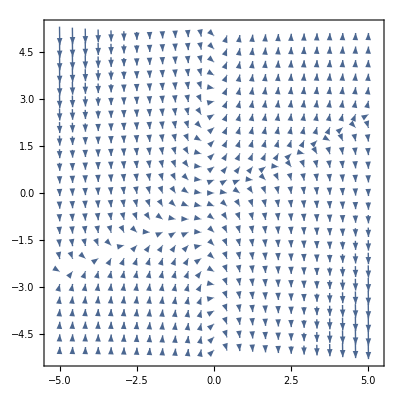

```mathematica
VectorPlot[
{1,2x y - x^2 +Sin[y]},
{x,-5,5},
{y,-5,5},
VectorPoints->Fine
]
```

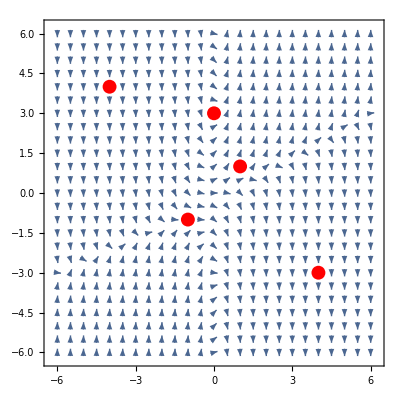

```mathematica
l=6;

func=Function[{m},VectorPlot[{1/Sqrt[1+m[x,y]^2],m[x,y]/Sqrt[1+m[x,y]^2]},{x,-l,l},{y,-l,l},VectorPoints->Fine,VectorScale->{0.01625,0.1}]];

Show[{
func@Function[{x,y},2x y - x^2 +Sin[y]],
Graphics[{
{PointSize[0.025],Red,Point[{{1,1},{-1,-1},{0,3},{4,-3},{-4,4}}]}
}]
}]
```

```mathematica
?VectorScale
```

VectorScale is an option to VectorPlot, ListVectorPlot, and related functions that determines the length and arrowhead size of field vectors that are drawn.

```mathematica
?CellularAutomaton
```

CellularAutomaton[rule,init,t] generates a list representing the evolution of the cellular automaton with the specified rule from initial condition init for t steps. 
CellularAutomaton[rule,init] gives the result of evolving init for one step. 
CellularAutomaton[rule,init,{tspec,xspec,…}] gives only those parts of the evolution specified by tspec, xspec, etc. 
CellularAutomaton[rule,init,{t,All,…}] includes at each step all cells that could be affected over the course of t steps. 
CellularAutomaton[rule] is an operator form of CellularAutomaton that represents one step of evolution.

{{y→InterpolatingFunction[{{0., 2.}}, <>]}}

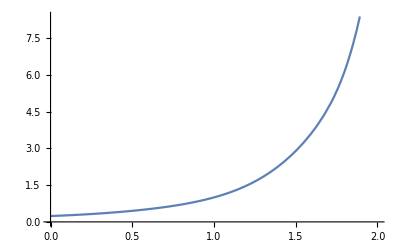

```mathematica
s=NDSolve[{y'[x]==2x y[x] - x^2 +Sin[y[x]],y[1]==1},y,{x,0,2}]
Plot[Evaluate[y[x]/.s],{x,0,2}]
```

```mathematica
?NDSolve
```

NDSolve[eqns,u,{x,x_min,x_max}] finds a numerical solution to the ordinary differential equations eqns for the function u with the independent variable x in the range x_min to x_max. 
NDSolve[eqns,u,{x,x_min,x_max},{y,y_min,y_max}] solves the partial differential equations eqns over a rectangular region.
NDSolve[eqns,u,{x,y}∈Ω] solves the partial differential equations eqns over the region Ω.
NDSolve[eqns,u,{t,t_min,t_max},{x,y}∈Ω] solves the time-dependent partial differential equations eqns over the region Ω.
NDSolve[eqns,{u_1,u_2,…},…] solves for the functions u_i.

```mathematica
DSolve[{y'[x]==3 Sec[x]^2 (1+y[x]^2),y[0]==1},y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→Tan[π/4+3 Tan[x]]}}

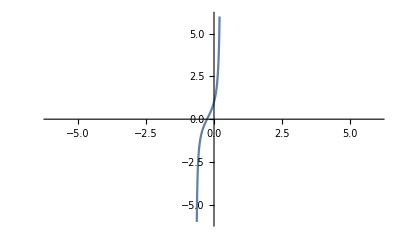

```mathematica
Plot[Tan[π/4+3 Tan[x]],{x,-ArcTan[π/4],ArcTan[π/12]},PlotRange->{{-6,6},{-6,6}}]
```

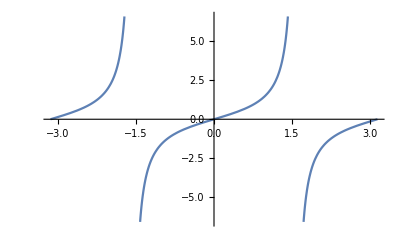

```mathematica
Plot[Tan[x],{x,-Pi,Pi}]
```

```mathematica
Reduce[-Pi/2<π/4+3 Tan[x]<Pi/2&&-Pi/2<x<Pi/2,x]/.{C[1]->0}
```

-ArcTan[π/4]<x<ArcTan[π/12]

```mathematica
D[Log[Log[x]],x]
```

1/(x Log[x])

```mathematica
Exp[-3Log[Log[x]]]
```

1/Log[x]^3

```mathematica
DSolve[{x y'[x]-(3/Log[x]) y[x]==2x^2 Log[x]^3,y[E]==E+E^2},y[x],x]
```

{{y[x]→ⅇ Log[x]^3+x^2 Log[x]^3}}

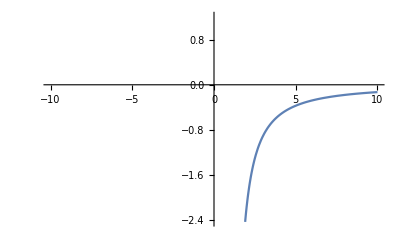

```mathematica
Plot[-3/(x Log[x]),{x,-10,10}]
```

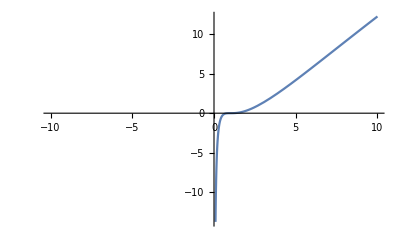

```mathematica
Plot[Log[x]^3,{x,-10,10}]
```

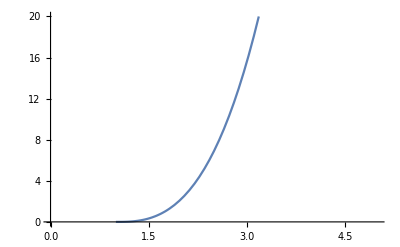

```mathematica
Plot[ⅇ Log[x]^3+x^2 Log[x]^3,{x,0,E+1},PlotRange->{{0,5},{0,20}}]
```

```mathematica
E+E^2//N
```

10.1073

```mathematica
{k}=NDSolve[{y'[x]==(4+2x)/(4+4y[x]^3),y[0]==1},y,{x,-4,4}]
```

{{y→InterpolatingFunction[{{-4., 4.}}, <>]}}

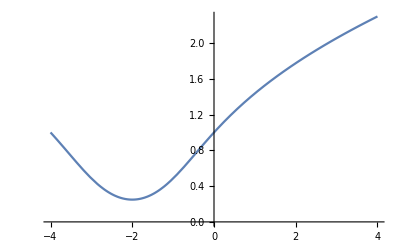

1.

```mathematica
Plot[k[[1,2]][x],{x,-4,4}]
k[[1,2]][0]
```

```mathematica
ClearAll[x,y]
```

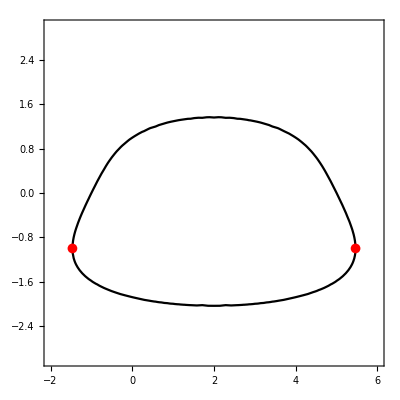

```mathematica
cp=ContourPlot[y^4+4y==-x^2+4x+5,{x,-2,6},{y,-3,3},
ContourStyle->Black,
Epilog->{
{Red,PointSize[0.0175],Point[{2+2Sqrt[3],-1}]},
{Red,PointSize[0.0175],Point[{2-2Sqrt[3],-1}]}
}]
```

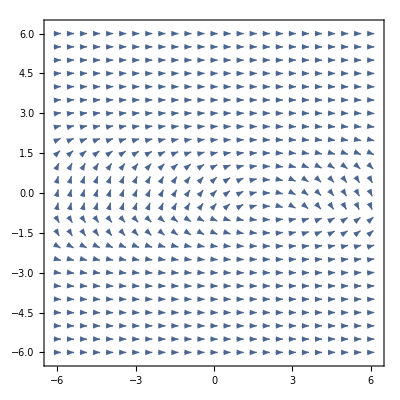

```mathematica
sl=func@Function[{x,y},(4-2x)/(4+4y^3)]
```

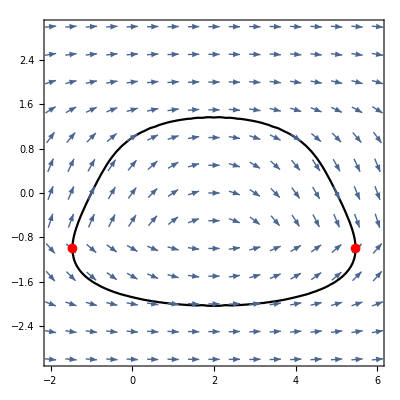

```mathematica
Show[{
cp,
sl
}]
```

```mathematica
ArcTan[1]
```

π/4

```mathematica
Sort@Table[N[{ArcTan[1/3(-Pi/2-(Pi/4+n Pi))],ArcTan[1/3(Pi/2-(Pi/4 + n Pi))]}],{n,-10,10}]
```

{{-1.4822,-1.47317},{-1.47317,-1.46209},{-1.46209,-1.4482},{-1.4482,-1.43026},{-1.43026,-1.40622},{-1.40622,-1.3724},{-1.3724,-1.32145},{-1.32145,-1.23658},{-1.23658,-1.07128},{-1.07128,-0.665774},{-0.665774,0.256053},{0.256053,0.918431},{0.918431,1.16942},{1.16942,1.28501},{1.28501,1.34978},{1.34978,1.39087},{1.39087,1.41918},{1.41918,1.43984},{1.43984,1.45556},{1.45556,1.46793},{1.46793,1.4779}}

```mathematica
{-0.6657737500283538,0.25605276998075555}
```

{-0.665774,0.256053}

```mathematica
ArcTan[-Pi/4]//N
ArcTan[Pi/12]//N
```

-0.665774

0.256053

```mathematica
elts=FiniteGroupData[{"DihedralGroup",7},"Generators"]
```

{2,8}

```mathematica
elts=DihedralGroup[7]//GroupElements
```

{Cycles[{}],Cycles[{{2,7},{3,6},{4,5}}],Cycles[{{1,2},{3,7},{4,6}}],Cycles[{{1,2,3,4,5,6,7}}],Cycles[{{1,3},{4,7},{5,6}}],Cycles[{{1,3,5,7,2,4,6}}],Cycles[{{1,4},{2,3},{5,7}}],Cycles[{{1,4,7,3,6,2,5}}],Cycles[{{1,5},{2,4},{6,7}}],Cycles[{{1,5,2,6,3,7,4}}],Cycles[{{1,6},{2,5},{3,4}}],Cycles[{{1,6,4,2,7,5,3}}],Cycles[{{1,7,6,5,4,3,2}}],Cycles[{{1,7},{2,6},{3,5}}]}

```mathematica
PermutationProduct[elts[[3]],{1,4,2,5,3,6,7}]
```

Cycles[{{1,4,6,5,3,7,2}}]

```mathematica
Exp[Integrate[-3/(x Log [x]),x]]
```

1/Log[x]^3

```mathematica
D[% *y[x],x]
```

-(3 y[x])/(x Log[x]^4)+y'[x]/Log[x]^3

```mathematica
DSolve[x y'[x]-(3/Log[x])y[x]==2 x^2 Log[x]^3,y[x],x]/.{C[1]->C}
```

{{y[x]→C Log[x]^3+x^2 Log[x]^3}}

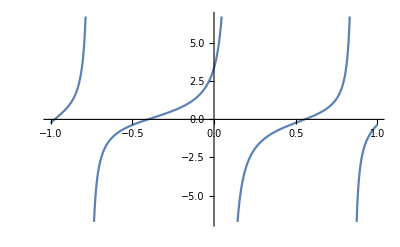
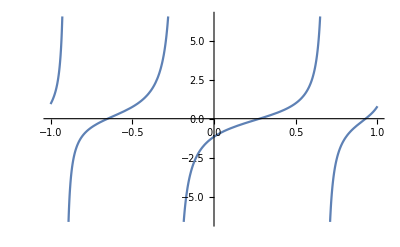
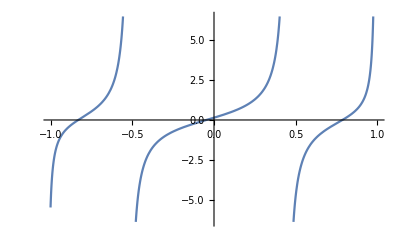
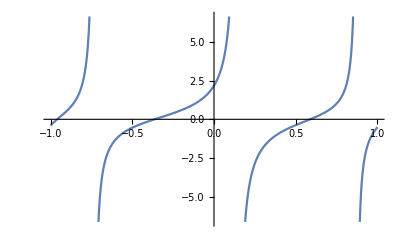
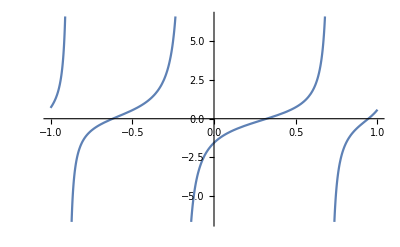
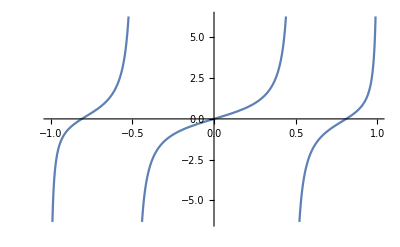
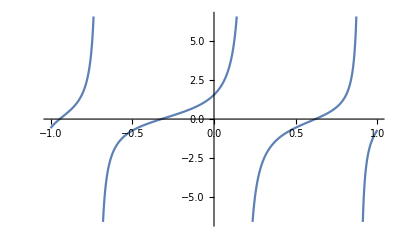
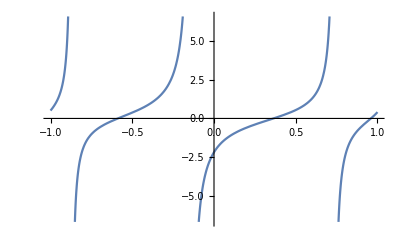

```mathematica
Table[Plot[Tan[3Tan[x]+C],{x,-1,1}],{C,-5,5,1}]
```

```mathematica
?Table
```

Table[expr,n] generates a list of n copies of expr. 
Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
Table[expr,{i,i_min,i_max}] starts with i=i_min. 
Table[expr,{i,i_min,i_max,di}] uses steps di. 
Table[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Table[expr,{i,i_min,i_max},{j,j_min,j_max},…] gives a nested list. The list associated with i is outermost.

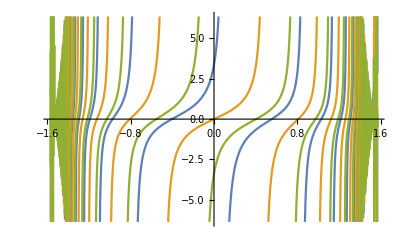

```mathematica
Plot[Evaluate[Table[Tan[3Tan[x]+C],{C,-5,5,5}]],{x,-Pi/2,Pi/2}]
```

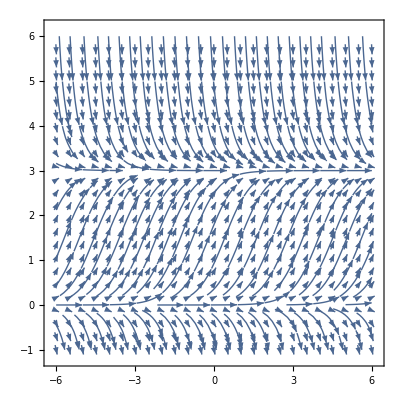

```mathematica
l=6;
func=Function[{m},StreamPlot[{1/Sqrt[1+m[x,y]^2],m[x,y]/Sqrt[1+m[x,y]^2]},{x,-l,l},{y,-1,l},VectorPoints->Fine,VectorScale->{0.01625,0.1}]];

func@Function[{x,y},2(1-y/3)y]
```

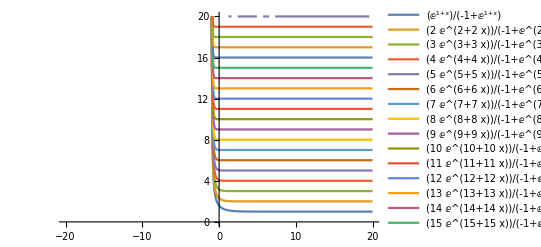

```mathematica
log=DSolve[y'[x]==r (1 - y[x]/K) y[x],y[x],x];

(* log=log/.{r->1.25,K->10}; *)
log=log[[1,1,2]];
log=log/.C[1]->1;

Plot[Evaluate[Table[log/.{K->k,r->k},{k,1,20,1}]],{x,-20,20},PlotRange->{0,20},PlotLegends->"Expressions"]
```

```mathematica
log2=DSolve[y'[x]==r (1 - y[x]/k) y[x],y[x],x];
log2=log2[[1,1,2]]
Plot[Evaluate[Table[log2/.{k->t},{t,1,20,1}]],{x,-20,20},PlotRange->{0,20},PlotLegends->"Expressions"]
```

(ⅇ^(r x+k C[1]) k)/(-1+ⅇ^(r x+k C[1]))

-Graphics-

```mathematica
log2
```

(ⅇ^(r x+k C[1]) k)/(-1+ⅇ^(r x+k C[1]))

```mathematica
ClearAll[r,K,c,x,y]
```

```mathematica
log2=DSolve[{y'[x]==2 (1 - y[x]/2) y[x]&&y[3]==2},y,x]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{}

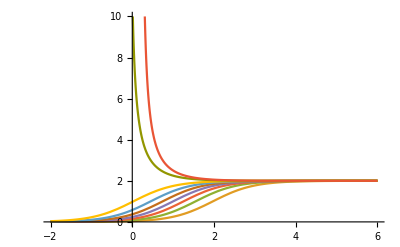

```mathematica
Quiet@Table[Quiet@DSolveValue[{y'[x]==2(1-y[x]/2) y[x],y[1]==C},y[x],x],{C,0,2.5,0.25}];
Quiet@Plot[%,{x,-2,6},PlotRange->{0,10}]
```

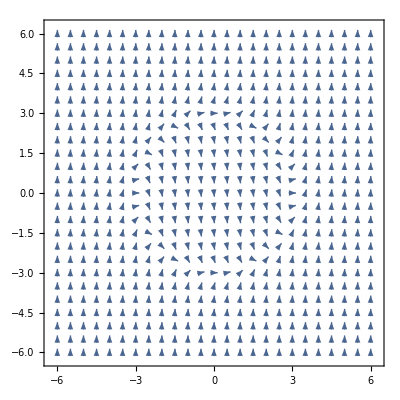

```mathematica
l=6;

func=Function[{m},VectorPlot[{1/Sqrt[1+m[x,y]^2],m[x,y]/Sqrt[1+m[x,y]^2]},{x,-l,l},{y,-l,l},VectorPoints->Fine,VectorScale->{0.01625,0.1}]];

Show[{
func@Function[{x,y},x^2+y^2-9]
}]
```

```mathematica
?VectorPlot
```

RowBox[{"VectorPlot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a vector plot of the vector field RowBox[{"{", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["y", "TI"]]}], "}"}] as a function of StyleBox["x", "TI"] and StyleBox["y", "TI"]. 
RowBox[{"VectorPlot", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["v", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["w", "TI"], StyleBox["x", "TI"]], ",", SubscriptBox[StyleBox["w", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several vector fields. 
RowBox[{"VectorPlot", "[", RowBox[{StyleBox["…", "TR"], ",", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}], "∈", StyleBox["reg", "TI"]}]}], "]"}] takes the variables RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "}"}] to be in the geometric region StyleBox["reg", "TI"].

```mathematica
?BesselJ
```

BesselJ[n,z] gives the Bessel function of the first kind J_n(z).

```mathematica
Apart[1/((y+a)(y+b)y),y]
```

1/(a b y)+1/(a (a-b) (a+y))-1/((a-b) b (b+y))

```mathematica
?Partial
```

Information::notfound: Symbol Partial not found.

```mathematica
Solve[1/((y+a)(y+b)y)==A/y+B/(y+1)+C/(y+b),{A,B,C}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{C→1/(y (a+y))-(A (b+y))/y-(B (b+y))/(1+y)}}

```mathematica
DSolve[{y'[x]==y[x]^3-9y[x],y[0]==2},y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{{y[x]→6/(√(4+5 ⅇ^(18 x)))}}

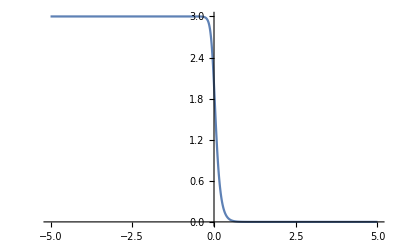

```mathematica
Plot[6/(√(4+5 ⅇ^(18 x))),{x,-5,5}]
```

```mathematica
ClearAll[y]
DSolve[y''''[x]-y'''[x]+y''[x]-y'[x]+y[x]==x,y[x],x]
```

{{y[x]→1+x+ⅇ^((1/4+(√5)/4) x) C[1] Cos[√(5/8-(√5)/8) x]+ⅇ^((1/4-(√5)/4) x) C[3] Cos[√(5/8+(√5)/8) x]+ⅇ^((1/4+(√5)/4) x) C[4] Sin[√(5/8-(√5)/8) x]+ⅇ^((1/4-(√5)/4) x) C[2] Sin[√(5/8+(√5)/8) x]}}

```mathematica
y=Sin[x]
```

Sin[x]

```mathematica
y=C[1]Sin[x]+Cos[x];
D[y,{x,4}]-D[y,{x,3}]+D[y,{x,2}]-D[y,{x,1}]
```

0

```mathematica
D[Log[ArcTan[x]],x]
```

1/((1+x^2) ArcTan[x])

```mathematica
Integrate[1/((1+x^2) ArcTan[x]),x]
```

Log[ArcTan[x]]

```mathematica
Integrate[x ArcTan[x],x]
```

-x/2+ArcTan[x]/2+1/2 x^2 ArcTan[x]

```mathematica
ClearAll[y]
```

```mathematica
DSolve[(x-x^3)y'[x]+(2x^2-1)y[x]-a x^3==0,y[x],x]
```

{{y[x]→a x+x √(1-x^2) C[1]}}

```mathematica
Exp[Integrate[(2x^2-1)/(x-x^3),x]]
```

1/(x √(1-x^2))

```mathematica
(x^3/(x-x^3)) 1/(x √(1-x^2))//FullSimplify
```

x/((1-x^2)^(3/2))

```mathematica
Integrate[x/((1-x^2)^(3/2)),x]
```

1/(√(1-x^2))

```mathematica
Solve[x-x^3==0,x]
```

{{x→-1},{x→0},{x→1}}

```mathematica
DSolve[{(x-x^3)y'[x]+(2x^2-1)y[x]-x^3==0,y[0.5]==3},y[x],x]
```

{{y[x]→5.7735 x (0.173205+1. √(1-x^2))}}

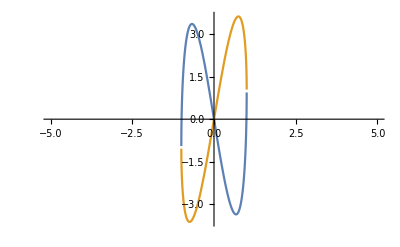

```mathematica
Plot[{-8.082903768654761 x (-0.12371791482634838+1. √(1-x^2)),5.773502691896258 x (0.1732050807568877+1. √(1-x^2))},{x,-5,5}]
```

```mathematica
DSolve[y'[x]==-r y[x],y[x],x]
```

{{y[x]→ⅇ^(-r x) C[1]}}

```mathematica
fn=Sin[x]+Cos[x]
```

Cos[x]+Sin[x]

```mathematica
D[fn,{x,3}]-D[fn,{x,2}]+D[fn,{x,1}]
```

Cos[x]+Sin[x]

```mathematica
CloudDeploy[FormFunction[{"f="->"MathExpression"},Plot3D[#f,{x,-5,5},{y,-5,5}]&],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/objects/7e63be9e-7b91-443e-a409-1479062ff360]

```mathematica
?CloudDeploy
```

CloudDeploy[expr] deploys expr to a new anonymous cloud object.
CloudDeploy[expr,uri] deploys expr to a cloud object at a given URI.
CloudDeploy[expr,CloudObject[uri]] deploys expr to a given cloud object.

```mathematica
CloudDeploy[FormFunction[{"f","f(x,y)="}->"MathExpression",Plot3D[#f,{x,-5,5},{y,-5,5}]&],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/objects/2551b3ab-3574-4593-922a-0b1833cab77a]

```mathematica
CloudDeploy[FormPage[{"f","f(x,y)="}->"MathExpression",Plot3D[#f,{x,-5,5},{y,-5,5}]&],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/objects/2483917a-468d-49db-90b8-f9b7633b9bcb]

```mathematica
FormPage[{{"name","what's your name?"}->"GivenName","gender"->TemplateIf[TemplateSlot["name"][[-1,-1]]=="male",{"Male","Female"},{"Female","Male"}]}]
```